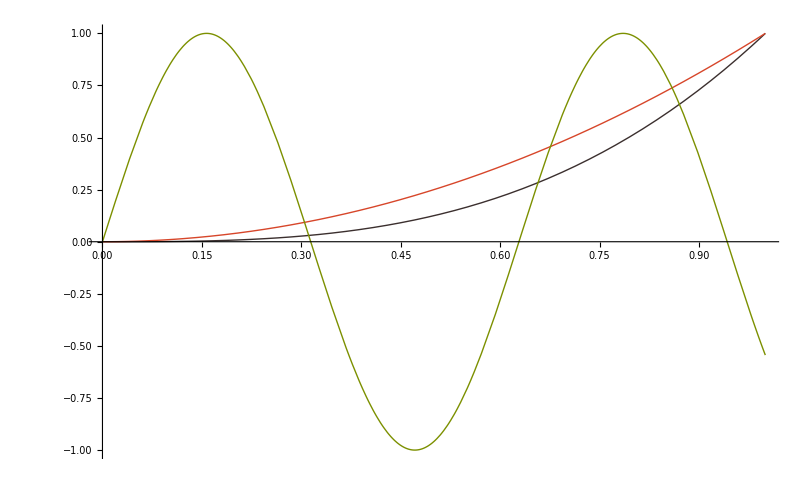

```mathematica
Plot[{x^3,x^2,Sin[10x]},{x,0,1},ColorFunction->Function[{x,y},If[Abs[y-x^2]<10^-5,Hue[x],If[Abs[y-x^3]<10^-5,GrayLevel[.8x],RGBColor[x,y,0]]]],ColorFunctionScaling->False,PlotStyle->Thick,PlotRange->All]
```